# Hintermaier and Koeniger

## Model Definition

State vars unconstrained dd,xx,yy, non state cc (constrained add kappa and eta)

```mathematica
uFunc[cc_?numbSymb,dd_?numbSymb]:= ((psiFunc[cc,dd]^(1-sigma))-1)/(1-sigma)
psiFunc[cc_?numbSymb,dd_?numbSymb]:=(cc^theta)*(dd+epsilonD)^(1-theta)
numbSymb[xx_]:=Or[NumberQ[xx],Head[xx]===Symbol,MatchQ[xx,_Symbol[t]],MatchQ[xx,_Symbol[t+1]],MatchQ[xx,_Symbol[t-1]]]
bigPsi[ddPrime_?numbSymb,dd_?numbSymb]:=0*((alpha/2)*(((ddPrime-(1-delta)*dd)/dd)^2)*dd)
```

```mathematica
sub5=D[uFunc[cc[t],dd[t-1]],cc[t]]->Simplify[(for1=(-kappa[t]*(1+rr)+D[uFunc[cc[t],dd[t-1]],cc[t]]-(1+rr)*beta*D[uFunc[cc[t+1],dd[t]],cc[t+1]]))-D[uFunc[cc[t],dd[t-1]],cc[t]]];
```

```mathematica
hAndKEqns={for1,
(-eta[t]-kappa[t]*mu*(1-delta)+D[uFunc[cc[t],dd[t-1]],cc[t]]*(1+D[bigPsi[dd[t],dd[t-1]],dd[t]])-((1-delta)*beta*D[uFunc[cc[t+1],dd[t]],cc[t+1]]+beta*(D[uFunc[cc[t+1],dd[t]],dd[t]]-D[uFunc[cc[t+1],dd[t]],cc[t+1]]*D[bigPsi[dd[t],dd[t-1]],dd[t]])))/.sub5,aa[t+1]+dd[t]+cc[t]+bigPsi[dd[t],dd[t-1]]-(xx[t-1]+yy[t]),xx[t]-((1+rr)*aa[t+1]+(1-delta)*dd[t]),(yy[t]-yMean)-rho*(yy[t-1]-yMean),xx[t]- (cnst0[t]+-gamma*yMin+(1-mu)*(1-delta)*dd[t]),dd[t]-(cnst1[t]+dMin)};
```

```mathematica
basicParamSubs=N[{sigma->2,rr->3/100,delta->2/100,yMin->9/100,gamma->95/100,mu->97/100,alpha ->5/100,dMin->1/100,yMean->1,rho->95/100,epsilonD->1/1000000}];
```

```mathematica
autoCorr95adjC0=N[{theta->8092/10000,beta->9391/10000}];
```

```mathematica
hAndKEqns/.basicParamSubs/.autoCorr95adjC0/.kappa[t]->0/.eta[t]->0;
```

```mathematica
D[uFunc[cc[t],dd[t-1]],cc[t]]
```

theta cc[t]^(-1+theta) (epsilonD+dd[-1+t])^(1-theta) (cc[t]^theta (epsilonD+dd[-1+t])^(1-theta))^-sigma

```mathematica
forMUc=D[uFunc[cc[t],dd[t-1]],cc[t]]/.basicParamSubs/.autoCorr95adjC0
```

(0.8092 (1.×10^-6+dd[-1+t])^0.1908)/(cc[t]^0.1908 (cc[t]^0.8092 (1.×10^-6+dd[-1+t])^0.1908)^2.)

```mathematica
FullForm[forMUc//N]
```

Times[0.8092,Power[cc[t],-0.1908],Power[Times[Power[cc[t],0.8092],Power[Plus[1.×10^-6,dd[Plus[-1.,t]]],0.1908]],-2.],Power[Plus[1.×10^-6,dd[Plus[-1.,t]]],0.1908]]

```mathematica
forMUd=D[uFunc[cc[t],dd[t-1]],dd[t-1]]/.basicParamSubs/.autoCorr95adjC0
```

(0.1908 cc[t]^0.8092)/((cc[t]^0.8092 (1.×10^-6+dd[-1+t])^0.1908)^2. (1.×10^-6+dd[-1+t])^0.8092)

```mathematica
N[Rational[3,4]]
```

0.75

```mathematica
{forMUc,forMUd}/.{dd[t-1]->0.009593126,cc[t]->.00448238}
```

{34832.1,3837.12}

```mathematica
hAndKEqns[[1]] /. basicParamSubs /. autoCorr95adjC0 /. kappa[t] -> 0 /. eta[t] -> 0
```

0.+(0.8092 (1.×10^-6+dd[-1+t])^0.1908)/(cc[t]^0.1908 (cc[t]^0.8092 (1.×10^-6+dd[-1+t])^0.1908)^2.)-(0.782717 (1.×10^-6+dd[t])^0.1908)/(cc[1+t]^0.1908 (cc[1+t]^0.8092 (1.×10^-6+dd[t])^0.1908)^2.)

```mathematica
for1
```

theta cc[t]^(-1+theta) (epsilonD+dd[-1+t])^(1-theta) (cc[t]^theta (epsilonD+dd[-1+t])^(1-theta))^-sigma-beta (1+rr) theta cc[1+t]^(-1+theta) (epsilonD+dd[t])^(1-theta) (cc[1+t]^theta (epsilonD+dd[t])^(1-theta))^-sigma-(1+rr) kappa[t]

### Mathematica Routines

#### newWeightedStochasticBasis

```mathematica
(*create a projection model and generate java code*)
newWeightedStochasticBasis[hAndKMod,(hAndKEqns)/.basicParamSubs/.autoCorr95adjC0(*/.kappa[t]->0/.eta[t]->0*)];
```

#### GenerateModelCode

```mathematica
{{stateVars,nonStateVars,noShocks},modEqns}=GenerateModelCode[hAndKMod];
```

c:/RSMA/Sun/SDK/jdk/bin/javac @S:/tryBenchWindows/projectionJLinkWin/javaSource/theArgs  -target 1.5 ./hAndKMod.java

```mathematica
{stateVars,nonStateVars}
```

{{dd,xx,yy},{aa,cc,cnst0,cnst1,eta,kappa}}

```mathematica
basicParamSubs
```

{sigma→2.,rr→0.03,delta→0.02,yMin→0.09,gamma→0.95,mu→0.97,alpha→0.05,dMin→0.01,yMean→1.,rho→0.95,epsilonD→1.×10^-6}

#### GenerateBasis

```mathematica
(*create chebyshev polynomials for projection*)(*define the range for capital*)polyRanges=N[{{ddLow=0*dMin,ddHigh=20},{xxLow=0,xxHigh=50},{yyLow=0.3,yyHigh=1.7}}/.basicParamSubs];
polyRanges=Table[{0,2},{3}]
(*initial power of polynomial*)
initPowers={0,0,0};
hAndKBasis=GenerateBasis[{stateVars,nonStateVars},polyRanges,initPowers]
```

{{0,2},{0,2},{0,2}}

«JavaObject[gov.frb.ma.msu.ProjectionTools.WeightedStochasticBasis]»

```mathematica
initPowers
```

{0,0,0}

```mathematica
polyRanges
```

{{0,2},{0,2},{0,2}}

```mathematica
guessWts={{.5},{.5},{1},{1},{1},{0},{0},{0},{0}};
guessWts={{10},{20},{1.},{5},{8},{0},{0},{0},{0}};(*
res00=ComputeInitialCollocationWeights[hAndKBasis,guessWts,modEqns];*)
```

```mathematica
hkm=JavaNew["hAndKMod"]
```

«JavaObject[hAndKMod]»

```mathematica
doVal[theVal_?NumberQ]:=Module[{},hAndKBasis[setAllWeights[{{theVal},{.20},{.1},{5},{8},{0},{0},{0},{0}}]];
valDrv00=hkm[updateValDrv[hAndKBasis]];
valDrv00[getTheVal[]][getRowPackedCopy[]][[{2,6,7}]]]
```

```mathematica
doVal[dVal_?NumberQ,xVal_?NumberQ,yVal_?NumberQ,aVal_?NumberQ,cVal_?NumberQ,cnst0Val_?NumberQ,cnst1Val_?NumberQ,etaVal_?NumberQ,kappaVal_?NumberQ]:=Module[{},hAndKBasis[setAllWeights[{{dVal},{xVal},{yVal},{aVal},{cVal},{cnst0Val},{cnst1Val},{etaVal},{kappaVal}}]];
valDrv00=hkm[updateValDrv[hAndKBasis]];
valDrv00[getTheVal[]][getRowPackedCopy[]][[{2,6,7}]]]
```

```mathematica
justTwo=Identity[(hAndKEqns)/.basicParamSubs/.autoCorr95adjC0][[2]](*/.kappa[t]->0/.eta[t]->0*)
```

-(0.17918 cc[1+t]^0.8092)/((cc[1+t]^0.8092 (1.×10^-6+dd[t])^0.1908)^2. (1.×10^-6+dd[t])^0.8092)-(0.744721 (1.×10^-6+dd[t])^0.1908)/(cc[1+t]^0.1908 (cc[1+t]^0.8092 (1.×10^-6+dd[t])^0.1908)^2.)-eta[t]+1.03 (-0.75992/(cc[1+t] (cc[1+t]^0.8092 (1.×10^-6+dd[t])^0.1908)^1.)-kappa[t])-0.9506 kappa[t]

```mathematica
Variables/@((hAndKEqns)/.basicParamSubs/.autoCorr95adjC0)
```

{{cc[t]^0.1908,cc[1+t]^0.1908,(cc[t]^0.8092 (1.×10^-6+dd[-1+t])^0.1908)^2.,(1.×10^-6+dd[-1+t])^0.1908,(cc[1+t]^0.8092 (1.×10^-6+dd[t])^0.1908)^2.,(1.×10^-6+dd[t])^0.1908,kappa[t]},{cc[1+t]^0.1908,cc[1+t]^0.8092,cc[1+t],(cc[1+t]^0.8092 (1.×10^-6+dd[t])^0.1908)^1.,(cc[1+t]^0.8092 (1.×10^-6+dd[t])^0.1908)^2.,(1.×10^-6+dd[t])^0.1908,(1.×10^-6+dd[t])^0.8092,eta[t],kappa[t]},{aa[1+t],cc[t],dd[t],xx[-1+t],yy[t]},{aa[1+t],dd[t],xx[t]},{yy[-1+t],yy[t]},{cnst0[t],dd[t],xx[t]},{cnst1[t],dd[t]}}

```mathematica
justTwoSS=justTwo/.xx_[t+_.]->xx
```

-(0.17918 cc^0.8092)/((cc^0.8092 (1.×10^-6+dd)^0.1908)^2. (1.×10^-6+dd)^0.8092)-(0.744721 (1.×10^-6+dd)^0.1908)/(cc^0.1908 (cc^0.8092 (1.×10^-6+dd)^0.1908)^2.)-eta+1.03 (-0.75992/(cc (cc^0.8092 (1.×10^-6+dd)^0.1908)^1.)-kappa)-0.9506 kappa

```mathematica
Chop[justTwoSS//N]
```

-(0.17918 cc^0.8092)/((cc^0.8092 (1.×10^-6+dd)^0.1908)^2. (1.×10^-6+dd)^0.8092)-(0.744721 (1.×10^-6+dd)^0.1908)/(cc^0.1908 (cc^0.8092 (1.×10^-6+dd)^0.1908)^2.)-1. eta+1.03 (-0.75992/(cc (cc^0.8092 (1.×10^-6+dd)^0.1908)^1.)-1. kappa)-0.9506 kappa

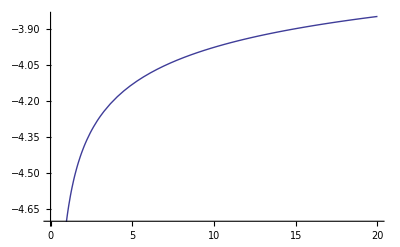

```mathematica
Plot[justTwoSS/.{kappa->1,eta->1,cc->1},{dd,0,20}]
```

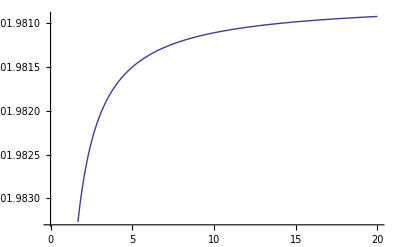

```mathematica
Plot[justTwoSS/.{kappa->1,eta->100,cc->100},{dd,0,20}]
```

```mathematica
polyRanges
```

{{0,2},{0,2},{0,2}}

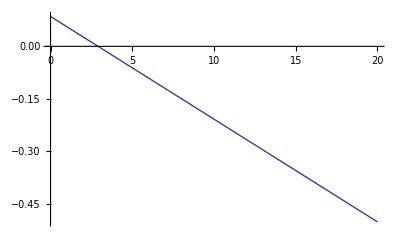

```mathematica
Reap[Plot[doVal[dd,999,999,999,40,999,999,10,10][[2]],{dd,0,20}(*,EvaluationMonitor:>Sow[{dd,doVal[dd,0,-1,999,999,0,0,0,0][[2]]}]*)]]
```

```mathematica
hAndKBasis
```

«JavaObject[gov.frb.ma.msu.ProjectionTools.WeightedStochasticBasis]»

```mathematica
doVal[3]
```

{-0.0377802,0.1973,2.99}

```mathematica
doDrv[dVal_?NumberQ,xVal_?NumberQ,yVal_?NumberQ,aVal_?NumberQ,cVal_?NumberQ,cnst0Val_?NumberQ,cnst1Val_?NumberQ,etaVal_?NumberQ,kappaVal_?NumberQ]:=Module[{},hAndKBasis[setAllWeights[{{dVal},{xVal},{yVal},{aVal},{cVal},{cnst0Val},{cnst1Val},{etaVal},{kappaVal}}]];
valDrv00=hkm[updateValDrv[hAndKBasis]];
valDrv00[getTheJac[]][getArray[]][[{1,6,7}]]]
```

```mathematica
doVal[11,.4,.3,999,999,0,0,0,0]
```

{-0.0000421614,0.1621,10.99}

```mathematica
doDrv[1,1,1,999,999,0,0,0,0][[2,1]]
```

-0.0294

FindRoot::jsing: Encountered a singular Jacobian at the point {xx} = {18.4}. Try perturbing the initial point(s).

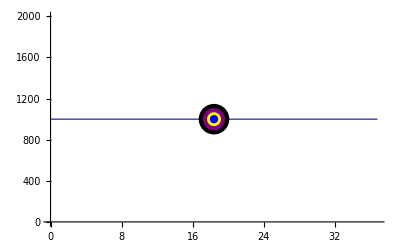
{{{xx→18.4},{Steps→1,Residual→1,Jacobian→1},-Graphics-},{}}

```mathematica
Reap[FindRootPlot[doVal[xx,999,999,999,40,999,999,10,10][[2]],{xx,18.4},Method->Newton,DampingFactor->1,AccuracyGoal->80,WorkingPrecision->40,MaxIterations->100000,Jacobian:>hip(*,AccuracyGoal->100,PrecisionGoal->10000,WorkingPrecision->18,EvaluationMonitor:>Sow[{xx,doVal[xx,1,5,999,999,0,0,0,0][[2]],hip[xx]}]*)]]
```

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

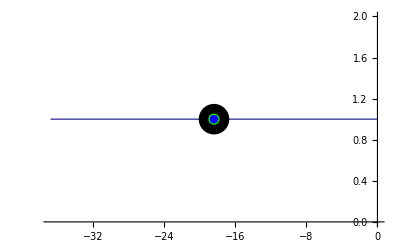
{{{1.,{xx→-18.4}},{Function→1},-Graphics-},{}}

```mathematica
Reap[FindMinimumPlot[(doVal[xx,1,5,999,999,0,0,0,0][[2]])^2,{xx,-18.4},DampingFactor->1,AccuracyGoal->Infinity,MaxIterations->100000(*,Jacobian:>hip,AccuracyGoal->100,PrecisionGoal->10000,WorkingPrecision->18,EvaluationMonitor:>Sow[{xx,doVal[xx,1,5,999,999,0,0,0,0][[2]],hip[xx]}]*)]]
```

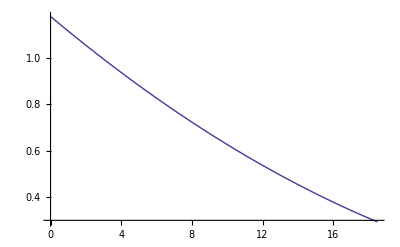
{-Graphics-,{{{3.77551×10^-7,0.0855},{0.36313,0.074824},{0.756805,0.0632499},{1.12439,0.0524429},{1.48477,0.0418479},{1.87569,0.0303548},{2.24052,0.0196287},{2.6359,0.00800468},{3.02406,-0.0034074},{3.38614,-0.0140525},{3.77876,-0.0255956},{4.1453,-0.0363717},{4.50462,-0.0469358},{4.89449,-0.0583979},{5.25827,-0.0690931},{5.65259,-0.0806862},{6.03971,-0.0920674},{6.40073,-0.102682},{6.7923,-0.114194},{7.15778,-0.124939},{7.55381,-0.136582},{7.94263,-0.148013},{8.30536,-0.158677},{8.69863,-0.17024},{9.06581,-0.181035},{9.42579,-0.191618},{9.8163,-0.203099},{10.1807,-0.213814},{10.5757,-0.225426},{10.9635,-0.236826},{11.3251,-0.247459},{11.7174,-0.258991},{12.0835,-0.269755},{12.4424,-0.280307},{12.8319,-0.291758},{13.1953,-0.302441},{13.5892,-0.314022},{13.957,-0.324837},{14.3177,-0.335439},{14.7088,-0.346939},{15.0739,-0.357673},{15.4695,-0.369304},{15.8579,-0.380723},{16.2203,-0.391376},{16.6131,-0.402926},{16.9799,-0.41371},{17.3395,-0.424281},{17.7296,-0.43575},{18.0936,-0.446453},{18.5,-0.4584},{0.181565,0.080162},{18.2968,-0.452426},{0.0907828,0.082831},{18.1952,-0.44944},{18.3984,-0.455413},{0.0453916,0.0841655},{18.1444,-0.447946},{18.3476,-0.45392},{18.4492,-0.456907},{0.022696,0.0848327},{18.119,-0.4472},{18.3222,-0.453173},{18.4238,-0.45616},{18.4746,-0.457653},{0.0113482,0.0851664},{18.1063,-0.446826},{18.3095,-0.4528},{18.4111,-0.455787},{18.4619,-0.45728},{18.4873,-0.458027},{0.00567428,0.0853332},{18.1,-0.44664},{18.3032,-0.452613},{18.4048,-0.4556},{18.4556,-0.457093},{18.481,-0.45784},{18.4937,-0.458213}}}}

```mathematica
Reap[Plot[(doVal[dd,1,5,999,999,0,0,0,0][[2]])^2,{dd,0,18.5},EvaluationMonitor:>Sow[{dd,doVal[dd,0,-1,999,999,0,0,0,0][[2]]}]]]
```

```mathematica
Clear[FindRootPlot];Remove[FindRootPlot];
<<Optimization`UnconstrainedProblems`
```

```mathematica
Options[FindRoot]
```

{AccuracyGoal→Automatic,Compiled→Automatic,DampingFactor→1,Evaluated→True,EvaluationMonitor→None,Jacobian→Automatic,MaxIterations→100,Method→Automatic,PrecisionGoal→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}

```mathematica
hip=Function[xx,With[{duh={{doDrv[xx,1,5,999,999,0,0,0,0][[2,1]]}}},duh]]
```

Function[xx,With[{duh={{doDrv[xx,1,5,999,999,0,0,0,0]⟦2,1⟧}}},duh]]

```mathematica
hipSq=Function[xx,With[{duh=2*doVal[xx,1,5,999,999,0,0,0,0][[2]]*{{doDrv[xx,1,5,999,999,0,0,0,0][[2,1]]}}},duh]]
```

Function[xx,With[{duh=2 doVal[xx,1,5,999,999,0,0,0,0]⟦2⟧ {{doDrv[xx,1,5,999,999,0,0,0,0]⟦2,1⟧}}},duh]]

```mathematica
Function[xx,With[{duh={{doDrv[xx,1,5,999,999,0,0,0,0]⟦1,1⟧}}},duh]]
```

Function[xx,With[{duh={{doDrv[xx,1,5,999,999,0,0,0,0]⟦1,1⟧}}},duh]]

```mathematica
hip[.1]//FullForm
```

List[List[-0.0294]]

```mathematica
Reap[huh=FindRoot[Cos[xx],{xx,1},EvaluationMonitor:>Sow[xx]]]
```

{{xx→1.5708},{{1.,1.64209,1.57068,1.5708,1.5708}}}

```mathematica
huh
```

{xx→1.5708}

```mathematica
Options[FindRoot]
```

{AccuracyGoal→Automatic,Compiled→Automatic,DampingFactor→1,Evaluated→True,EvaluationMonitor→None,Jacobian→Automatic,MaxIterations→100,Method→Automatic,PrecisionGoal→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}

```mathematica
doVal[16]
```

{-0.0221361,-0.1849,15.99}

```mathematica
Methods[valDrv00[getTheVal[]]]
```

Jama.Matrix arrayLeftDivideEquals(Jama.Matrix)
Jama.Matrix arrayLeftDivide(Jama.Matrix)
Jama.Matrix arrayRightDivideEquals(Jama.Matrix)
Jama.Matrix arrayRightDivide(Jama.Matrix)
Jama.Matrix arrayTimesEquals(Jama.Matrix)
Jama.Matrix arrayTimes(Jama.Matrix)
Jama.CholeskyDecomposition chol()
Object clone()
double cond()
static Jama.Matrix constructWithCopy(double[][])
Jama.Matrix copy()
double det()
Jama.EigenvalueDecomposition eig()
boolean equals(Object)
double[][] getArray()
double[][] getArrayCopy()
Class getClass()
int getColumnDimension()
double[] getColumnPackedCopy()
double get(int, int)
Jama.Matrix getMatrix(int[], int[])
Jama.Matrix getMatrix(int[], int, int)
Jama.Matrix getMatrix(int, int, int[])
Jama.Matrix getMatrix(int, int, int, int)
int getRowDimension()
double[] getRowPackedCopy()
int hashCode()
static Jama.Matrix identity(int, int)
Jama.Matrix inverse()
Jama.LUDecomposition lu()
Jama.Matrix minusEquals(Jama.Matrix)
Jama.Matrix minus(Jama.Matrix)
double norm1()
double norm2()
double normF()
double normInf()
void notify()
void notifyAll()
Jama.Matrix plusEquals(Jama.Matrix)
Jama.Matrix plus(Jama.Matrix)
void print(int, int)
void print(java.io.PrintWriter, int, int)
void print(java.io.PrintWriter, java.text.NumberFormat, int)
void print(java.text.NumberFormat, int)
Jama.QRDecomposition qr()
static Jama.Matrix random(int, int)
int rank()
static Jama.Matrix read(java.io.BufferedReader) throws java.io.IOException
void set(int, int, double)
void setMatrix(int, int, int, int, Jama.Matrix)
void setMatrix(int[], int, int, Jama.Matrix)
void setMatrix(int, int, int[], Jama.Matrix)
void setMatrix(int[], int[], Jama.Matrix)
Jama.Matrix solve(Jama.Matrix)
Jama.Matrix solveTranspose(Jama.Matrix)
Jama.SingularValueDecomposition svd()
Jama.Matrix times(double)
Jama.Matrix timesEquals(double)
Jama.Matrix times(Jama.Matrix)
String toString()
double trace()
Jama.Matrix transpose()
Jama.Matrix uminus()
void wait(long, int) throws InterruptedException
void wait(long) throws InterruptedException
void wait() throws InterruptedException

```mathematica
Methods[valDrv00]
```

gov.frb.ma.msu.ProjectionTools.EquationValDrv augSys(gov.frb.ma.msu.ProjectionTools.EquationValDrv) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
void chkNan(double[][], String) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
gov.frb.ma.msu.ProjectionTools.EquationValDrv divide(double) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
gov.frb.ma.msu.ProjectionTools.EquationValDrv divide(gov.frb.ma.msu.ProjectionTools.EquationValDrv) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
boolean equals(Object)
gov.frb.ma.msu.ProjectionTools.EquationValDrv exp() throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
Class getClass()
int getNumNodes()
Jama.Matrix getTheJac()
Jama.Matrix getTheVal()
double getZeroThreshold()
int hashCode()
gov.frb.ma.msu.ProjectionTools.EquationValDrv log() throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
gov.frb.ma.msu.ProjectionTools.EquationValDrv minus(double) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
gov.frb.ma.msu.ProjectionTools.EquationValDrv minus(gov.frb.ma.msu.ProjectionTools.EquationValDrv) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
void notify()
void notifyAll()
gov.frb.ma.msu.ProjectionTools.EquationValDrv plus(double) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
gov.frb.ma.msu.ProjectionTools.EquationValDrv plus(gov.frb.ma.msu.ProjectionTools.EquationValDrv) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
gov.frb.ma.msu.ProjectionTools.EquationValDrv pow(double) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
gov.frb.ma.msu.ProjectionTools.EquationValDrv pow(int) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
void print()
void setNumNodes(int)
void setTheJac(Jama.Matrix)
void setTheVal(Jama.Matrix)
void setZeroThreshold(double)
gov.frb.ma.msu.gsmin.ValueDerivative stackCnstrns()
gov.frb.ma.msu.gsmin.ValueDerivative sumSq()
gov.frb.ma.msu.ProjectionTools.EquationValDrv times(double) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
gov.frb.ma.msu.ProjectionTools.EquationValDrv times(gov.frb.ma.msu.ProjectionTools.EquationValDrv) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
String toString()
void wait(long, int) throws InterruptedException
void wait(long) throws InterruptedException
void wait() throws InterruptedException

```mathematica
Methods[hkm]
```

boolean equals(Object)
Class getClass()
double[] getParams()
int hashCode()
void noNans(gov.frb.ma.msu.ProjectionTools.WeightedStochasticBasis, double[][], double[][]) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
void notify()
void notifyAll()
String toString()
void updateParams(double[])
gov.frb.ma.msu.ProjectionTools.EquationValDrv updateValDrv(gov.frb.ma.msu.ProjectionTools.StochasticBasis) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
void wait(long, int) throws InterruptedException
void wait(long) throws InterruptedException
void wait() throws InterruptedException

```mathematica
Methods[hAndKBasis]
```

static int[][] allPowers(int[])
static int[] dropEnd(int[])
boolean equals(Object)
static int[] expand(int[], int, int)
Class getClass()
Jama.Matrix getDrvPolyNowDrvMatrix(int, int, int)
Jama.Matrix getDrvPolyNowValMatrix(int, int, int)
double[] getGaussHermiteMean()
double[] getGaussHermiteStDev()
int getMaxShrink()
java.util.List getNewtonIters()
gov.frb.ma.msu.ProjectionTools.StrategyIterSequenceInfo getNewtonItersSeq()
int getNewtonSteps()
int getNumberOfShocks()
double[][] getRanges()
int[] getShockVarLocs()
double getShrinkFactor()
gov.frb.ma.msu.ProjectionTools.GaussHermite getTheGaussHermite()
gov.frb.ma.msu.ProjectionTools.NonStateVariablePolynomials getTheNonState()
double[] getTheShockVals()
gov.frb.ma.msu.ProjectionTools.StateVariablePolynomials getTheState()
int getVarIndex(gov.frb.ma.msu.ProjectionTools.VarTime) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
int hashCode()
gov.frb.ma.msu.ProjectionTools.Basis incPowers(gov.frb.ma.msu.ProjectionTools.StateVariablePolynomials, int[]) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
gov.frb.ma.msu.ProjectionTools.WeightedStochasticBasis incPowers(int[]) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
static int indexPower(int[], int, int[])
boolean isInNeedOfShockUpdatesQ()
boolean isPerfectForesightQ()
void multiArrayCopy(double[][], double[][])
void notify()
void notifyAll()
int numNodesNow()
int numVarsNow()
static int[] rawPows(int)
void setAllWeights(double[][])
void setAllWeights(int)
void setGaussHermiteMean(double[])
void setGaussHermiteStDev(double[])
void setInNeedOfShockUpdatesQ(boolean)
void setMaxShrink(int)
void setNewtonIters(java.util.List)
void setNewtonItersSeq(gov.frb.ma.msu.ProjectionTools.StrategyIterSequenceInfo)
void setNewtonSteps(int)
void setNumberOfShocks(int)
void setPerfectForesightQ(boolean)
void setShockVarLocs()
void setShockVarLocs(int[])
void setShrinkFactor(double)
void setTheGaussHermite(gov.frb.ma.msu.ProjectionTools.GaussHermite)
void setTheNonState(gov.frb.ma.msu.ProjectionTools.NonStateVariablePolynomials)
void setTheNonStateWeights(double[][]) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
void setTheShockVals(double[])
void setTheState(gov.frb.ma.msu.ProjectionTools.StateVariablePolynomials)
void setTheStateWeights(double[][]) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
double[][][] solveParamsRange(double[][], gov.frb.ma.msu.ProjectionTools.DoEqns, double[], double[], int) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
String toString()
void updateForShocks(gov.frb.ma.msu.ProjectionTools.DoEqns, int[], double[]) throws gov.frb.ma.msu.ProjectionTools.ProjectionRuntimeException
double[] updateParams(double[], double[], int, int)
void wait(long, int) throws InterruptedException
void wait(long) throws InterruptedException
void wait() throws InterruptedException

```mathematica
res00[getResWeights[]]
```

res00[getResWeights[]]

```mathematica
res01=ComputeCollocationWeightsToOrder[res00,{0,0,0}];
```

```mathematica
res01[getResWeights[]]
```

ComputeCollocationWeightsToOrder[res00,{0,0,0}][getResWeights[]]

```mathematica
forSteady=(((hAndKEqns) /. basicParamSubs /. autoCorr95adjC0 /. kappa[t] -> 0 /. eta[t] -> 0)/.xx_[t+_.]->xx)
```

{0.+(0.0264827 (1.×10^-6+dd)^0.1908)/(cc^0.1908 (cc^0.8092 (1.×10^-6+dd)^0.1908)^2.),0.-0.782717/(cc (cc^0.8092 (1.×10^-6+dd)^0.1908)^1.)-(0.17918 cc^0.8092)/((cc^0.8092 (1.×10^-6+dd)^0.1908)^2. (1.×10^-6+dd)^0.8092)-(0.744721 (1.×10^-6+dd)^0.1908)/(cc^0.1908 (cc^0.8092 (1.×10^-6+dd)^0.1908)^2.),aa+cc+dd-xx-yy,-1.03 aa-0.98 dd+xx,-1.-0.95 (-1.+yy)+yy,0.0855-cnst0-0.0294 dd+xx,-0.01-cnst1+dd}

```mathematica
numSSSubs=Join[ basicParamSubs , autoCorr95adjC0 ,{ kappa[t] -> 0 , eta[t] -> 0,xx_[t+_.]->xx}]
```

{sigma→2.,rr→0.03,delta→0.02,yMin→0.09,gamma→0.95,mu→0.97,alpha→0.05,dMin→0.01,yMean→1.,rho→0.95,epsilonD→1.×10^-6,theta→0.8092,beta→0.9391,kappa[t]→0,eta[t]→0,xx_[t+_.]→xx}

```mathematica
kick=FindRoot[Thread[forSteady==0],{aa,1},{cc,1},{dd,.5},{xx,10},{yy,1}]
```

FindRoot::nlnum: The function value {0.0302272, -2.15244, -8.5, 8.48, 0., 10.0708  - 1.\ cnst0, 0.49  - 1.\ cnst1}
 is not a list of numbers with dimensions {7} at {aa, cc, dd, xx, yy} = {1., 1., 0.5, 10., 1.}.

FindRoot[Thread[forSteady==0],{aa,1},{cc,1},{dd,0.5},{xx,10},{yy,1}]

```mathematica
numSSSubs
```

{sigma→2.,rr→0.03,delta→0.02,yMin→0.09,gamma→0.95,mu→0.97,alpha→0.05,dMin→0.01,yMean→1.,rho→0.95,epsilonD→1.×10^-6,theta→0.8092,beta→0.9391,kappa[t]→0,eta[t]→0,xx_[t+_.]→xx}

```mathematica
forSteady/.kick
```

FindRoot::nlnum: The function value {0.0302272, -2.15244, -8.5, 8.48, 0., 10.0708  - 1.\ cnst0, 0.49  - 1.\ cnst1}
 is not a list of numbers with dimensions {7} at {aa, cc, dd, xx, yy} = {1., 1., 0.5, 10., 1.}.

ReplaceAll::reps: {FindRoot[Thread[forSteady == 0], {aa, 1}, {cc, 1}, {dd, 0.5}, {xx, 10}, {yy, 1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{0.+(0.0264827 (1.×10^-6+dd)^0.1908)/(cc^0.1908 (cc^0.8092 (1.×10^-6+dd)^0.1908)^2.),0.-0.782717/(cc (cc^0.8092 (1.×10^-6+dd)^0.1908)^1.)-(0.17918 cc^0.8092)/((cc^0.8092 (1.×10^-6+dd)^0.1908)^2. (1.×10^-6+dd)^0.8092)-(0.744721 (1.×10^-6+dd)^0.1908)/(cc^0.1908 (cc^0.8092 (1.×10^-6+dd)^0.1908)^2.),aa+cc+dd-xx-yy,-1.03 aa-0.98 dd+xx,-1.-0.95 (-1.+yy)+yy,0.0855-cnst0-0.0294 dd+xx,-0.01-cnst1+dd}/.FindRoot[Thread[forSteady==0],{aa,1},{cc,1},{dd,0.5},{xx,10},{yy,1}]

```mathematica
constrEqns={xx[t]≥ -gamma*yMin+(1-mu)*(1-delta)*dd[t],dd[t]≥dMin}
```

{xx[t]≥-gamma yMin+(1-delta) (1-mu) dd[t],dd[t]≥dMin}

```mathematica
notconstrEqns={ -gamma*yMin+(1-mu)*(1-delta)*dd[t],dd[t]≥dMin}
```

{-gamma yMin+(1-delta) (1-mu) dd[t],dd[t]≥dMin}

```mathematica
(notconstrEqns/.numSSSubs)/.kick
```

FindRoot::nlnum: The function value {0.0302272, -2.15244, -8.5, 8.48, 0., 10.0708  - 1.\ cnst0, 0.49  - 1.\ cnst1}
 is not a list of numbers with dimensions {7} at {aa, cc, dd, xx, yy} = {1., 1., 0.5, 10., 1.}.

ReplaceAll::reps: {FindRoot[Thread[forSteady == 0], {aa, 1}, {cc, 1}, {dd, 0.5}, {xx, 10}, {yy, 1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{-0.0855+0.0294 dd,dd≥0.01}/.FindRoot[Thread[forSteady==0],{aa,1},{cc,1},{dd,0.5},{xx,10},{yy,1}]

```mathematica
kick
```

FindRoot::nlnum: The function value {0.0302272, -2.15244, -8.5, 8.48, 0., 10.0708  - 1.\ cnst0, 0.49  - 1.\ cnst1}
 is not a list of numbers with dimensions {7} at {aa, cc, dd, xx, yy} = {1., 1., 0.5, 10., 1.}.

FindRoot[Thread[forSteady==0],{aa,1},{cc,1},{dd,0.5},{xx,10},{yy,1}]

```mathematica
forSteady[[3]]
```

aa+cc+dd-xx-yy

```mathematica
forSteady[[3]]/.kick
```

FindRoot::nlnum: The function value {0.0302272, -2.15244, -8.5, 8.48, 0., 10.0708  - 1.\ cnst0, 0.49  - 1.\ cnst1}
 is not a list of numbers with dimensions {7} at {aa, cc, dd, xx, yy} = {1., 1., 0.5, 10., 1.}.

ReplaceAll::reps: {FindRoot[Thread[forSteady == 0], {aa, 1}, {cc, 1}, {dd, 0.5}, {xx, 10}, {yy, 1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

aa+cc+dd-xx-yy/.FindRoot[Thread[forSteady==0],{aa,1},{cc,1},{dd,0.5},{xx,10},{yy,1}]

## Initialization

```mathematica
Needs["JLink`"]
```

```mathematica
laptop[]:=Block[{},
SetDirectory["c:/User Data/forProj/projRepo/projection/generatedModels"];
$Path=PrependTo[$Path,"c:/User Data/forProj/projRepo/projection"];AddToClassPath["c:/User Data/forProj/projRepo/projection/target/test-classes","c:/tryRep/gov/frb/ma/msu/projection/1.0-SNAPSHOT/projection-1.0-SNAPSHOT.jar","c:/tryRep/gov/frb/ma/msu/commons-math/1.0-SNAPSHOT/commons-math-1.0-SNAPSHOT.jar","c:/tryRep/gov/frb/ma/msu/Jama-1.0.2/1.0-SNAPSHOT/Jama-1.0.2-1.0-SNAPSHOT.jar","c:/User Data/forProj/projRepo/projection/generatedModels"]; "laptop"]
```

```mathematica
desktop[]:=Module[{},SetDirectory["g:/RES2/ProjectionMethodTools/projection/generatedModels"];
$Path=PrependTo[$Path,"G:/RES2/ProjectionMethodTools/projection"];AddToClassPath["G:/RES2/ProjectionMethodTools/projection/target/test-classes","s:/tryRep/gov/frb/ma/msu/projection/1.0-SNAPSHOT/projection-1.0-SNAPSHOT.jar","s:/tryRep/gov/frb/ma/msu/commons-math/1.0-SNAPSHOT/commons-math-1.0-SNAPSHOT.jar","s:/tryRep/gov/frb/ma/msu/Jama-1.0.2/1.0-SNAPSHOT/Jama-1.0.2-1.0-SNAPSHOT.jar","g:/RES2/ProjectionMethodTools/projection/generatedModels"];"desktop"]
```

```mathematica
linux[]:=Module[{},SetDirectory["/msu/res2/m1gsa00/ProjectionMethodTools/projection/generatedModels"];PrependTo[$Path,"/msu/res2/m1gsa00/ProjectionMethodTools/projection/generatedModels"];AddToClassPath[
ReinstallJava[CommandLine->"/msu/scratch2/m1gsa00/jdk1.7.0/bin/java"];"/msu/home/m1gsa00/RES2/ProjectionMethodTools/projection/target/test-classes","/msu/scratch/m1gsa00/tryRep/gov/frb/ma/msu/projection/1.0-SNAPSHOT/projection-1.0-SNAPSHOT.jar","/msu/scratch/m1gsa00/tryRep/gov/frb/ma/msu/commons-math/1.0-SNAPSHOT/commons-math-1.0-SNAPSHOT.jar","/msu/scratch/m1gsa00/tryRep/gov/frb/ma/msu/Jama-1.0.2/1.0-SNAPSHOT/Jama-1.0.2-1.0-SNAPSHOT.jar","/msu/res2/m1gsa00/ProjectionMethodTools/projection/generatedModels"];"linux"]
```

```mathematica
If[$OperatingSystem=="Windows",
If[$MachineName=="lt-m1gsa00",laptop[],desktop[]],linux[]]
Needs["ProjectionInterface`"]
(*prepSCE2011[]*)
```

desktop

```mathematica
(*Needs["ProjectionInterface`"];*)pre="gov.frb.ma.msu.ProjectionTools.";(*InstallJava[];*)
```

```mathematica
(*ReinstallJava[]*)
```